```mathematica
(*Código utilizado para obtener las secciones de Poincaré del sistema dada una energía y un k. Basado en el código fuente de Mathematica https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/poincare-sections.html. Adaptado al problema por Gustavo Ardila y Cristian Tibambre*)

(*Primero lo hacemos con k=0.5*)
```

```mathematica
(*Constantes y parametro de control*)
k0=0.5;
m=5;
g=9.8;

(*Ecuaciones diferenciales*)
ecuaciones={p'[s]==-k0*(Sin[h[s]]-Sin[j[s]])*Cos[h[s]]-m*g*Sin[h[s]], h'[s]==p[s]/m, q'[s]==k0*(Sin[h[s]]-Sin[j[s]])*Cos[j[s]]-m*g*Sin[j[s]], j'[s]==q[s]/m};
(*Guarda la sección dada la solucion obtenida usando NDSolve y si esta cumple ciertas condiciones. Aqui se usa E*)
(*poinca[{h0_,j0_,p0_,q0_}]:=Reap[NDSolve[{ecuas, h[0]==h0, j[0]==j0, p[0]==p0, q[0]==q0 , WhenEvent[j[t]==0&& q[t]≠0, Sow[{h[t],p[t]}]]},{h[t], j[t], p[t],q[t]},{t,0,1000}, MaxSteps->Infinity]][[-1,1]];*)
secciones[{a0_,b0_,c0_,d0_}]:=Reap[NDSolve[{ecuaciones, h[0]==a0, j[0]==b0, p[0]==c0, q[0]==d0, WhenEvent[q[s]==0, Sow[{h[s],p[s]}]]},{h[s],j[s], p[s], q[s]},{s,0,1000}, MaxSteps->Infinity]][[-1,1]];
```

```mathematica
(*Calcula la sección*)
```

```mathematica
info= Map[secciones, bunch]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{7.49578,14.8901},{4.65101,3.89598},{6.94788,-21.0146},{7.17041,19.4519},631,{5.36247,18.6968},{5.63734,-21.4129},{7.89926,7.28576}},385,{1}}
 |  |  |  |

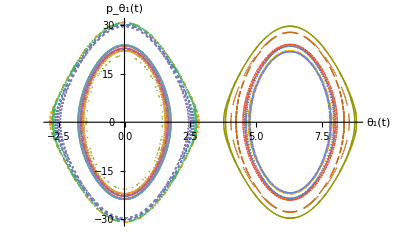

```mathematica
ListPlot[{ info[[1]],info[[3]], info[[6]],info[[8]],info[[13]],info[[14]],info[[15]],info[[19]],info[[30]],info[[31]],info[[32]],info[[34]],info[[41]],info[[42]],info[[46]],info[[47]],info[[48]],info[[50]]}, ImageSize->Full, AxesLabel->{Style["θ_1(t)", Bold,20,Black], Style["p_θ_1(t)", Bold,20,Black]}]
```

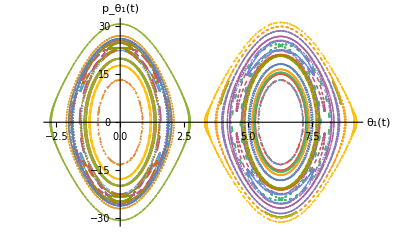

-Graphics-

```mathematica
1
```

```mathematica
info[[101]]
```

{{3.04229,-1.77036},{0.163953,-31.1383},{-2.93495,-0.456156},{-0.391042,30.5817},{3.00623,2.23884},{3.40358,4.09368},{7.79075,22.5338},{9.19258,-2.19984},{5.26018,-27.3089},{3.17906,-1.56918},{1.94718,-17.5407},{-2.79563,-6.1018},{-4.05232,-13.9767},{-8.96349,-7.94474},{-10.4073,-15.0954},{-15.2971,-7.61938},{-17.1342,-20.826},{-21.7739,-6.20141},{-24.7058,-31.0882},{-28.4078,-6.64507},{-33.0409,-22.6175},{-35.5309,-16.2329},{-40.5106,-8.39748},{-43.7067,-31.6317},{-47.2421,-5.88322},{-51.6631,-24.3294},{-53.7651,-7.14827},{-58.608,-16.4608},{-60.1468,-7.97069},{-65.0602,-14.0598},{-66.3694,-6.87527},{-71.2002,-15.8022},{-72.3969,-3.0431},{-76.1454,-29.0338},{-78.3807,0.193775},{-75.8569,30.4172},{-72.3673,2.7862},{-70.9887,18.5595},{-66.2849,5.94967},{-64.6736,19.1644},{-59.9675,6.22546},{-57.6568,26.9687},{-53.4579,5.69951},{-49.611,30.3244},{-46.6826,9.55449},{-41.6279,13.8354},{-39.088,24.9843},{-34.6391,6.18701},{-30.835,30.4285},{-28.0588,5.94635},{-23.4563,21.2024},{-21.6645,6.35705},{-16.908,17.7878},{-15.4926,4.35424},{-11.1524,23.6799},{-9.50636,0.246831},{-10.6656,-18.0253},{-15.3671,-5.72323},{-16.298,-9.28907},{-21.2457,-11.4531},{-22.1817,-3.53464},{-26.2745,-26.1624},{-28.1073,0.790457},{-25.131,31.2935},{-22.0624,2.48935},{-20.4084,22.2857},{-15.9283,5.08913},{-13.8841,24.9791},{-9.55051,5.36204},{-6.33604,31.7835},{-2.94515,6.85969},{1.80363,20.5466},{4.18723,17.0324},{9.12029,7.91234},{12.2415,31.4597},{15.7885,5.38159},{20.001,26.5244},{22.2104,5.26358},{26.7166,22.0549},{28.3928,3.20262},{32.0928,29.4661},{34.4277,0.357599},{32.6914,-24.9964},{28.4752,-3.92592},{27.283,-14.966},{22.4155,-7.30114},{21.089,-13.9303},{16.1697,-8.06894},{14.6072,-16.7164},{9.7732,-7.08236},{7.60735,-25.0613},{3.23867,-5.86926},{-0.422463,-31.2646},{-3.52011,-8.92179},{-8.54207,-15.0945},{-11.0702,-23.9622},{-15.6077,-6.43546},{-19.409,-30.5613},{-22.2278,-6.31205},{-26.9045,-20.1529},{-28.6981,-7.75945},{-33.5985,-14.7768},{-35.0291,-8.07864},{-39.9476,-13.741},{-41.201,-6.30665},{-45.9707,-17.0187},{-47.1814,-1.84281},{-49.707,-30.0887},{-53.2033,-1.33763},{-51.3845,26.3144},{-47.3222,3.319},{-46.7493,5.88687},{-42.0117,17.0264},{-41.0199,-1.83463},{-44.5832,-29.9663},{-47.1168,-2.5799},{-49.6362,-29.8976},{-53.365,-4.31082},{-56.6525,-31.6578},{-59.8583,-6.11988},{-64.4653,-22.3193},{-66.7712,-13.7062},{-71.8059,-9.27329},{-74.4279,-28.3069},{-78.4943,-5.07212},{-82.0407,-31.0691},{-84.8777,-3.72376},{-88.44,-30.4886},{-91.0421,-1.66845},{-91.7441,-9.94002},{-96.7215,-10.3926},{-97.465,-1.87509},{-100.314,-31.221},{-103.652,-3.7085},{-106.776,-31.6074},{-110.058,-5.33003},{-114.378,-25.7912},{-116.8,-10.5878},{-121.864,-11.8338},{-124.202,-24.0725},{-128.669,-5.6485},{-131.864,-31.6218},{-135.107,-3.89854},{-138.525,-31.0805},{-141.316,-2.07191},{-142.587,-17.9715},{-147.297,-5.26256},{-147.211,6.45037},{-142.405,15.0092},{-141.739,-4.8741},{-146.414,-18.1396},{-147.554,0.353614},{-145.725,25.6665},{-141.64,2.31294},{-143.418,-26.4373},{-147.44,-2.95634},{-147.326,5.02328},{-142.666,19.0358},{-141.247,3.22962},{-137.436,29.135},{-134.931,4.91949},{-130.558,24.6084},{-128.341,8.97992},{-123.328,13.508},{-121.306,18.7335},{-116.517,6.55791},{-114.089,27.9275},{-110.071,3.9988},{-107.814,27.6676},{-103.848,3.0418},{-103.441,3.85476},{-99.1107,23.9592},{-97.2238,4.30684},{-92.9622,25.4689},{-90.7796,6.96802},{-85.9213,17.1973},{-83.9972,13.6723},{-78.9977,8.73936},{-76.9145,23.2612},{-72.4499,4.99213},{-70.3102,26.1489},{-66.1567,3.63419},{-65.2155,11.8082},{-60.2483,8.81423},{-59.5532,2.73402},{-55.8613,29.668},{-53.313,4.05971},{-49.3616,28.5738},{-46.8418,6.73419},{-42.031,18.4593},{-39.9757,14.333},{-34.9826,8.54911},{-32.6546,26.023},{-28.402,4.73002},{-25.7181,30.2246},{-22.0931,3.03921},{-20.5315,21.0168},{-16.0014,4.35291},{-16.0582,-5.07506},{-20.6967,-18.4657},{-21.6631,4.01915},{-17.1337,20.4234},{-15.8005,-0.0363749},{-17.2066,-21.2712},{-21.6753,-3.72499},{-20.587,19.8249},{-16.0292,4.64156},{-15.987,-4.15678},{-20.465,-21.7876},{-22.0987,-3.19415},{-25.8134,-29.7794},{-28.4245,-4.95328},{-32.7865,-24.8059},{-35.0322,-9.15982},{-40.0532,-13.2942},{-42.1077,-19.3688},{-46.8642,-6.39846},{-49.3739,-28.6306},{-53.3067,-3.91752},{-55.6742,-28.5454},{-59.5278,-2.85382},{-59.9392,-4.11853},{-64.357,-22.8632},{-66.1508,-4.37978},{-70.4599,-24.9029},{-72.59,-7.00754},{-77.4548,-17.0096},{-79.3572,-13.5377},{-84.3584,-8.79197},{-86.4022,-22.7605},{-90.9015,-5.0683},{-92.9629,-25.3375},{-97.1926,-3.78795},{-98.0856,-10.9191},{-103.066,-9.57862},{-103.852,-3.43586},{-107.942,-26.7021},{-110.122,-4.6471},{-114.46,-24.7977},{-116.637,-7.98247},{-121.592,-15.0709},{-123.533,-16.1092},{-128.445,-7.47914},{-130.656,-25.4546},{-134.93,-4.45247},{-137.044,-26.1901},{-141.18,-3.45837},{-141.79,-6.7416},{-146.654,-15.2918},{-147.898,-4.79014},{-152.418,-21.9547},{-154.272,-6.71076},{-159.11,-17.2338},{-160.909,-11.6641},{-165.937,-10.0141},{-167.766,-19.0717},{-172.5,-5.98005},{-174.287,-21.6722},{-178.815,-4.71302},{-179.78,-11.1625},{-184.761,-9.43034},{-185.599,-4.43485},{-190.063,-22.4777},{-191.888,-5.47567},{-196.519,-20.7369},{-198.421,-9.15728},{-203.433,-12.825},{-205.258,-16.5493},{-210.135,-7.07113},{-212.083,-22.8256},{-216.549,-4.69732},{-218.029,-18.688},{-222.725,-5.34843},{-223.226,-3.08611},{-227.195,-27.6752},{-229.459,-4.11739},{-233.539,-27.4104},{-235.92,-6.82285},{-240.751,-17.9353},{-242.754,-14.0915},{-247.749,-8.6055},{-249.978,-24.9698},{-254.315,-4.79735},{-256.77,-28.8347},{-260.617,-3.2038},{-261.859,-16.6223},{-266.65,-5.96039},{-266.915,1.43984},{-264.053,31.1101},{-260.977,0.158037},{-263.875,-31.19},{-266.906,-1.6047},{-266.687,5.38648},{-261.972,18.1091},{-260.609,3.43738},{-256.653,28.0698},{-254.283,5.15296},{-249.806,23.2534},{-247.68,9.46559},{-242.652,12.7166},{-240.655,19.0815},{-235.891,6.3695},{-233.546,27.3224},{-229.47,3.96016},{-227.48,25.2538},{-223.268,3.49087},{-223.005,1.03751},{-221.088,25.9952},{-216.932,4.13645},{-214.984,24.5417},{-210.636,5.15214},{-207.753,31.0524},{-204.108,5.98722},{-199.666,24.8581},{-197.181,13.1161},{-192.119,9.89024},{-189.361,29.096},{-185.355,5.46825},{-181.419,29.1887},{-178.893,5.05265},{-174.502,23.7565},{-172.669,3.3656},{-168.911,29.1628},{-166.618,0.530746},{-167.97,-20.7526},{-172.508,-4.8836},{-173.5,-11.0579},{-178.456,-9.69551},{-179.455,-6.40658},{-184.243,-16.3914},{-185.34,-0.677425},{-185.75,-6.25177},{-190.571,-16.1217},{-191.814,-3.82879},{-195.998,-25.9788},{-198.151,-5.54382},{-202.765,-21.2447},{-204.762,-10.0781},{-209.799,-11.8086},{-211.741,-19.101},{-216.493,-6.2326},{-218.664,-25.7665},{-222.883,-4.06188},{-224.465,-20.5275},{-229.042,-4.67378},{-229.338,-0.383615},{-229.909,-8.72161},{-234.834,-11.7586},{-235.51,1.10524},{-232.851,30.7815},{-229.405,3.26897},{-227.037,28.726},{-223.111,4.66771},{-219.752,31.6515},{-216.565,6.61764},{-211.836,20.5843},{-209.539,15.6869},{-204.564,8.27895},{-201.725,30.1632},{-197.915,4.97938},{-194.122,29.8702},{-191.547,3.86285},{-187.743,29.1453},{-185.402,1.55075},{-184.564,12.1413},{-179.614,8.39562},{-179.146,-0.596769},{-180.855,-24.3343},{-185.078,-2.82036},{-183.671,23.0104},{-179.333,3.82419},{-179.236,-2.44721},{-182.962,-29.2665},{-185.408,-3.35264},{-188.888,-31.0022},{-191.779,-5.23504},{-196.179,-24.5887},{-198.466,-10.216},{-203.518,-12.0422},{-205.704,-22.1021},{-210.297,-5.8019},{-213.104,-30.5834},{-216.717,-3.6782},{-219.415,-30.5008},{-222.922,-2.35646},{-223.293,-3.9462},{-227.66,-23.4919},{-229.502,-4.25606},{-233.751,-25.5732},{-235.936,-6.82729},{-240.777,-17.542},{-242.703,-13.3335},{-247.712,-8.95511},{-249.78,-22.9399},{-254.27,-5.07896},{-256.418,-26.1746},{-260.571,-3.65737},{-261.568,-12.6445},{-266.517,-8.1942},{-267.144,-2.26111},{-270.468,-31.1263},{-273.358,-3.7658},{-276.927,-30.8139},{-279.792,-5.89605},{-284.401,-21.9469},{-286.599,-12.4498},{-291.647,-9.9292},{-293.992,-25.3869},{-298.327,-5.13996},{-301.323,-31.3082},{-304.694,-3.32283},{-307.274,-30.0234},{-310.864,-2.25319},{-310.746,3.98236},{-306.361,22.4075},{-305.012,-2.90435},{-309.257,-24.1049},{-310.946,-0.63641},{-310.592,6.6269},{-305.735,15.1889},{-304.6,3.10306},{-300.786,29.0361},{-298.311,4.62808},{-294.047,25.773},{-291.766,8.16915},{-286.797,14.9016},{-284.793,17.1998},{-279.923,7.12092},{-277.547,27.225},{-273.44,4.23025},{-271.07,28.4441},{-267.192,3.00631},{-266.514,8.2868},{-261.561,12.5623},{-260.542,4.09381},{-256.213,24.2762},{-254.226,5.53465},{-249.597,20.892},{-247.651,9.67639},{-242.624,12.2124},{-240.746,17.8704},{-235.931,6.59264},{-233.886,24.2376},{-229.533,4.36199},{-228.037,19.17},{-223.373,5.14087},{-222.965,1.75832},{-220.078,31.2874},{-216.792,3.57998},{-213.757,31.5237},{-210.407,5.13523},{-206.203,26.9786},{-203.705,9.78876},{-198.655,12.8398},{-196.364,22.8008},{-191.799,5.916},{-188.664,31.5646},{-185.336,4.04243},{-181.86,30.9481},{-179.11,2.24405},{-177.429,22.9947},{-173.058,3.6203},{-173.56,-11.4242},{-178.48,-8.7885},{-178.841,3.15462},{-174.665,25.3774},{-172.724,2.88141},{-169.407,31.3131},{-166.419,4.57769},{-162.346,27.8597},{-159.844,8.08129},{-154.882,15.4294},{-152.771,18.2332},{-147.939,6.93684},{-145.283,29.4526},{-141.433,4.18579},{-138.479,31.2557},{-135.173,2.56832},{-133.826,18.5978},{-129.147,5.08799},{-129.171,-5.27523},{-133.843,-17.8242},{-134.743,4.33303},{-130.151,19.4477},{-128.916,-0.396574},{-130.902,-27.0511},{-134.83,-1.84398},{-132.768,28.4587},{-128.995,2.45238},{-129.263,-7.01022},{-134.149,-14.2785},{-135.151,-1.92337},{-137.913,-31.0116},{-141.344,-3.80033},{-144.462,-31.6115},{-147.76,-5.4037},{-152.105,-25.5476},{-154.52,-10.8681},{-159.587,-11.5443},{-161.955,-24.6142},{-166.381,-5.5728},{-169.63,-31.64},{-172.814,-3.90058},{-176.284,-30.9219},{-179.019,-2.03952},{-180.312,-18.3016},{-185.003,-5.12866},{-184.877,6.96318},{-180.033,14.0284},{-179.438,-4.94121},{-184.121,-18.0623},{-185.27,0.0970331},{-183.922,20.5025},{-179.397,4.01287},{-180.336,-18.1059},{-184.996,-5.20964},{-185.077,4.09853},{-180.611,21.9372},{-178.969,3.1107},{-175.32,30.1231},{-172.651,4.84234},{-168.346,25.4776},{-166.054,8.87088},{-161.044,13.7792},{-158.984,19.0224},{-154.205,6.53776},{-151.674,28.7394},{-147.749,3.97676},{-145.263,29.3195},{-141.518,2.74853},{-140.963,6.55419},{-136.115,15.6277},{-134.863,4.53361},{-130.419,22.9672},{-128.497,6.42028},{-123.701,18.094},{-121.859,11.3626},{-116.826,10.3278},{-114.962,19.2848},{-110.236,5.974},{-108.348,22.8744},{-103.904,4.45608},{-102.839,12.9471},{-97.8939,8.05204},{-97.2043,3.43257},{-93.0964,26.4939},{-90.9453,4.5344},{-86.6454,25.2019},{-84.4471,7.69569},{-79.5146,15.6502},{-77.5735,15.541},{-72.6365,7.74853},{-70.4418,25.1328},{-66.1352,4.55484},{-63.9772,26.5471},{-59.8741,3.43042},{-59.1658,8.35216},{-54.21,12.4981},{-53.1808,4.34446},{-48.7672,23.2477},{-46.8576,5.7953},{-42.1666,19.8754},{-40.2773,10.0274},{-35.2458,11.7261},{-33.3958,17.9003},{-28.587,6.52132},{-26.6263,23.3482},{-22.2073,4.48763},{-20.8685,16.9166},{-16.0801,5.98186},{-15.5834,2.37212},{-12.1089,30.6494},{-9.37043,3.75292},{-5.7204,30.4343},{-2.9385,5.95199},{1.69616,21.4971},{3.86238,12.5068},{8.90723,9.8444},{11.2214,25.1108},{15.5753,5.12184},{18.4783,31.0542},{21.935,3.2782},{24.3034,28.785},{28.0995,2.51866},{27.9257,-5.15641},{23.2793,-18.4168},{22.2887,3.55555},{26.6994,22.1704},{28.2223,0.74634},{28.3167,0.604108},{29.5546,18.7005},{34.2058,4.77534},{33.6816,-12.8342},{28.7982,-7.69501},{28.5977,4.65851},{33.207,19.6686},{34.616,2.25052},{37.5461,31.3557},{40.8454,3.98805},{44.2988,31.2927},{47.3095,6.04641},{51.9327,21.8884},{54.1726,13.1971},{59.2119,9.48399},{61.69,26.9528},{65.8878,5.03248},{69.1367,31.577},{72.2551,3.38331},{75.243,31.3145},{78.4213,1.84059},{78.416,-1.72369},{75.3608,-31.1951},{72.4749,0.0865796},{75.4606,31.1958},{78.4213,1.63455},{78.4146,-1.95071},{75.1318,-31.1414},{72.2434,-3.39045},{69.0296,-31.5608},{65.8709,-5.10994},{61.6018,-26.1987},{59.1837,-9.81127},{54.1359,-12.6951},{51.8983,-22.2499},{47.3036,-5.91951},{44.3197,-31.2261},{40.8553,-3.87433},{37.6907,-31.4471},{34.6354,-2.18775},{33.5883,-14.7069},{28.7175,-6.79384},{28.4572,2.35474},{32.1627,28.9167},{34.3042,-1.66482},{30.4516,-27.663},{28.3831,-0.519322},{29.4644,17.488},{34.1763,5.13689},{33.5835,-14.1813},{28.7464,-6.86041},{28.6548,5.5804},{33.4096,17.0704},{34.5873,1.60468},{36.7644,27.9641},{40.7268,4.04313},{43.1847,29.0776},{47.0959,5.01099},{50.797,30.7555},{53.7358,7.97436},{58.6813,16.4834},{60.99,20.0252},{65.7555,6.811},{68.9518,31.6675},{72.3238,4.8304},{76.3405,28.0692},{78.6404,3.64969},{82.416,29.214},{84.7472,1.13152},{84.6487,-2.54627},{80.9156,-28.832},{78.7711,1.3462},{82.4172,29.1636},{84.7352,1.13003},{84.6675,-2.44771},{80.99,-29.5993},{78.4812,-3.49555},{74.9135,-30.7105},{72.0901,-5.4882},{67.59,-23.3301},{65.3656,-11.0099},{60.3086,-11.1476},{58.0918,-23.1425},{53.5773,-5.53141},{50.7598,-30.6777},{47.1824,-3.52018},{44.6538,-29.7046},{40.9935,-2.43814},{40.8927,0.572843},{42.2416,20.1676},{46.7968,4.21484},{46.0507,-15.5865},{41.2648,-6.23759},{41.1005,3.76818},{45.4766,23.1034},{47.2139,3.04632},{50.7745,30.5512},{53.5308,4.77562},{57.7825,26.0785},{60.1252,8.70574},{65.1271,14.1068},{67.2033,18.9541},{71.989,6.59946},{74.5659,29.0375},{78.4561,4.00795},{81.0757,30.0682},{84.6932,2.64053},{85.4029,9.13478},{90.3759,11.3912},{91.2741,3.36935},{95.3059,27.2733},{97.5543,4.70706},{101.901,24.7373},{104.084,8.19229},{109.054,14.707},{111.008,16.6486},{115.897,7.25982},{118.147,25.969},{122.372,4.34705},{124.502,26.3961},{128.615,3.38848},{129.173,5.98022},{133.96,17.0142},{135.325,4.81565},{139.839,22.1165},{141.724,7.00981},{146.596,16.5831},{148.395,12.3928},{153.414,9.4368},{155.268,19.884},{159.951,5.70157},{161.721,21.6489},{166.246,4.66644},{167.112,9.66644},{172.096,10.9075},{173.053,4.84362},{177.614,21.1771},{179.367,6.06041},{184.116,18.772},{185.924,10.0422},{190.953,11.6068},{192.736,17.055},{197.581,6.76082},{199.401,21.5012},{203.951,4.89556},{205.164,14.7539},{210.052,7.02389},{210.699,3.79115},{214.97,24.7663},{216.955,4.70489},{221.35,24.0207},{223.45,7.88586},{228.398,15.1286},{230.297,15.4239},{235.234,7.73637},{237.341,24.2037},{241.719,4.64711},{243.682,24.5684},{247.969,3.8143},{248.574,6.30651},{253.397,16.2718},{254.719,4.95815},{259.274,21.4954},{261.114,7.096},{265.995,16.3162},{267.773,12.3307},{272.791,9.45438},{274.614,19.4601},{279.321,5.80309},{281.035,20.8901},{285.612,4.86944},{286.467,9.3032},{291.448,11.345},{292.449,5.10684},{297.067,20.3429},{298.773,6.3859},{303.574,17.7982},{305.337,10.4403},{310.366,11.1168},{312.12,17.0784},{316.96,6.69472},{318.699,20.53},{323.31,5.11001},{324.415,12.9443},{329.363,8.10733},{330.123,4.53148},{334.623,21.9454},{336.396,5.35573},{341.005,21.0361},{342.909,8.80136},{347.908,13.3317},{349.723,15.9268},{354.628,7.34928},{356.563,22.4837},{361.058,4.81486},{362.589,19.2878},{367.252,5.16878},{367.779,3.68962},{372.029,24.9487},{374.018,4.45711},{378.32,25.0847},{380.488,7.37065},{385.391,16.2663},{387.311,14.5919},{392.282,8.20278},{394.401,24.0348},{398.801,4.7792},{400.907,25.9399},{405.075,3.60234},{405.864,9.46183},{410.843,11.066},{411.758,3.9914},{416.065,24.4862},{418.056,5.27614},{422.622,21.8109},{424.607,9.12334},{429.62,12.9825},{431.5,17.2014},{436.352,6.88176},{438.423,24.3482},{442.774,4.41793},{444.413,20.9749},{448.965,4.60705},{449.372,2.28491},{452.804,30.7841},{455.576,3.67242},{459.141,30.7958},{461.996,5.75337},{466.568,22.4295},{468.774,11.9429},{473.828,10.3211},{476.127,24.6452},{480.525,5.25993},{483.459,31.1381},{486.901,3.38515},{489.462,29.9146},{493.077,2.31565},{493.031,-2.86312},{489.092,-27.2468},{487.194,1.8673},{491.083,27.469},{493.144,0.846786},{492.793,-6.79149},{487.922,-14.8351},{486.824,-2.89357},{483.145,-29.838},{480.55,-4.40207},{476.426,-27.1865},{474.027,-7.61208},{469.105,-16.1632},{467.074,-16.369},{462.161,-7.52162},{459.753,-27.3142},{455.643,-4.36845},{453.055,-29.8068},{449.372,-2.87925},{448.317,-14.2097},{443.423,-7.13662},{443.019,0.338895},{444.162,17.6345},{448.874,5.18076},{448.442,-11.807},{443.536,-8.37662},{443.328,5.23235},{448.038,17.8575},{449.266,1.4799},{451.191,25.8327},{455.373,4.29392},{457.511,26.3676},{461.713,5.08731},{464.972,31.7756},{468.295,6.75529},{473.033,20.6252},{475.386,16.4821},{480.337,8.05544},{483.35,31.0622},{486.998,5.20313},{491.063,27.909},{493.396,4.64351},{497.679,24.8772},{499.553,2.26215},{502.193,30.4983},{505.611,1.41387},{504.113,-23.1096},{499.758,-4.11012},{499.053,-7.2363},{494.19,-14.2614},{493.31,0.489083}}

```mathematica
{{{h[s]->InterpolatingFunction[…][s],j[s]->InterpolatingFunction[…][s],p[s]->InterpolatingFunction[…][s],q[s]->InterpolatingFunction[…][s]}},{}}⟦-1,1⟧
```

Part::partw: Part 1 of {} does not exist.

{{{h[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],j[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],p[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],q[s]→InterpolatingFunction[{{0., 1000.}}, <>][s]}},{}}⟦-1,1⟧

1

```mathematica
datos={abcdt[[2]]}
```

{{{{h[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],j[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],p[s]→InterpolatingFunction[{{0., 1000.}}, <>][s],q[s]→InterpolatingFunction[{{0., 1000.}}, <>][s]}},{}}⟦-1,1⟧}

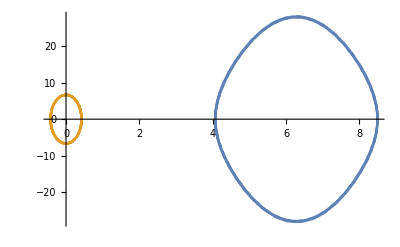

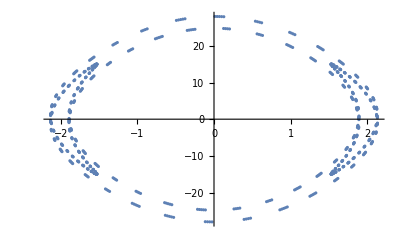

1

{{1.55238,-14.2901},{-1.52925,14.9848},{1.55933,-14.789},{-1.64089,13.7004},{1.76289,-11.7265},{-1.90449,8.92987},{2.03594,-5.44149},{-2.12164,1.3847},{2.12152,3.2758},{-1.985,-8.86223},{1.63594,15.8729},{-0.976126,-23.7767},{0.0116259,28.0104},{0.957318,-23.9385},{-1.6249,16.0474},{1.97985,-9.00218},{-2.12018,3.38908},{2.12274,1.28746},{-2.0385,-5.35651},{1.90767,8.85871},{-1.76595,-11.6725},{1.64324,13.6658},{-1.56062,-14.7745},{1.52933,14.9902},{-1.55131,-14.3156},{1.6196,12.742},{-1.71771,-10.266},{1.81891,6.91739},{-1.8863,-2.74342},{1.87313,-2.28371},{-1.71916,8.35959},{1.34428,-15.5996},{-0.67501,22.5685},{-0.215312,-24.5803},{1.02796,19.5545},{-1.55397,-12.0714},{1.81376,5.35194},{-1.89279,0.196697},{1.86152,-4.80905},{-1.77302,8.59863},{1.66928,-11.5426},{-1.58251,13.5952},{1.53456,-14.7442},{-1.53733,14.9995},{1.59357,-14.3642},{-1.69705,12.8358},{1.83192,-10.4436},{-1.97268,7.28703},{2.08628,-3.50897},{-2.13506,-0.825068},{2.0752,5.88258},{-1.84555,-12.1203},{1.35447,19.8147},{-0.52693,-26.7766},{-0.491267,26.9379},{1.3304,-20.1089},{-1.83292,12.3759},{2.07028,-6.08518},{-2.13509,0.994227},{2.08942,3.36136},{-1.9775,-7.15981},{1.83712,10.3415},{-1.70153,-12.7636},{1.59656,14.3243},{-1.53844,-14.9921},{1.53373,14.7692},{-1.57998,-13.6528},{1.66566,11.6331},{-1.76928,-8.72082},{1.85903,4.96111},{-1.89323,-0.379521},{1.8193,-5.13096},{-1.56757,11.8062},{1.05249,-19.2939},{-0.248256,24.5056},{-0.645231,-22.7628},{1.32535,15.8762},{-1.70994,-8.60352},{1.87042,2.48454},{-1.88755,2.57626},{1.8222,-6.77993},{-1.72153,10.1593},{1.62277,-12.6677},{-1.55305,14.2742},{1.5292,-14.9813},{-1.55854,14.798},{1.63943,-13.7219},{-1.76099,11.76},{1.9025,-8.97409},{-2.03433,5.49432},{2.12093,-1.44513},{-2.12233,-3.20547},{1.98815,8.77546},{-1.64273,-15.7645},{0.987746,23.6751},{-0.0260956,-28.008},{-0.94553,24.0383},{1.61794,-16.1563},{-1.9766,9.08963},{2.11931,-3.45978},{-2.1234,-1.22684},{2.04008,5.30353},{-1.90964,-8.8143},{1.76785,11.6387},{-1.64471,-13.6441},{1.56143,14.7653},{-1.52939,-14.9934},{1.55065,14.3312},{-1.61838,-12.7703},{1.71624,10.3068},{-1.81763,-6.97001},{1.8858,2.80743},{-1.87413,2.20684},{1.72262,-8.26624},{-1.35144,15.4932},{0.686372,-22.4919},{0.202615,24.6063},{-1.01842,-19.654},{1.54865,12.1737},{-1.81156,-5.43728},{1.89259,-0.126136},{-1.86246,4.75036},{1.77444,-8.55143},{-1.67067,11.5076},{1.58348,-13.5729},{-1.53489,14.7345},{1.53691,-15.0022},{-1.59242,14.3794},{1.69533,-12.8634},{-1.82992,10.4828},{1.97081,-7.33596},{-2.08504,3.56577},{2.13501,0.760027},{-2.07704,-5.80481},{1.85033,12.0223},{-1.36364,-19.7012},{0.540609,26.7118},{0.477438,-26.9975},{-1.32099,20.2222},{1.82796,-12.475},{-2.06833,6.16372},{2.13506,-1.05969},{-2.09061,-3.30427},{1.97935,7.11058},{-1.83912,-10.3019},{1.70326,12.7356},{-1.59773,-14.3087},{1.53889,14.989},{-1.53342,-14.7786},{1.57901,13.6749},{-1.66426,-11.6678},{1.76783,8.76784},{-1.85804,-5.01969},{1.89335,0.449945},{-1.82139,5.0459},{1.57274,-11.704},{-1.06187,19.1923},{0.26096,-24.474},{0.63363,22.8361},{-1.31793,-15.9832},{1.7063,8.69825},{-1.86932,-2.56251},{1.88801,-2.5114},{-1.82346,6.72656},{1.723,-10.1178},{-1.624,12.6388},{1.55373,-14.258},{-1.52917,14.9777},{1.55774,-14.8069},{-1.63796,13.7434},{1.75908,-11.7938},{-1.90049,9.01863},{2.0327,-5.5476},{-2.1202,1.50608},{2.12311,3.13459},{-1.99129,-8.68808},{1.64953,15.6553},{-0.999422,-23.5717},{0.0407144,28.0037},{0.933553,-24.1384},{-1.61086,16.2666},{1.97327,-9.17827},{-2.11841,3.53138},{2.12405,1.16549},{-2.04167,-5.24991},{1.91164,8.76931},{-1.76978,-11.6045},{1.6462,13.6221},{-1.56225,-14.7558},{1.52945,14.9965},{-1.55,-14.3469},{1.61716,12.7987},{-1.71476,-10.3478},{1.81633,7.02303},{-1.88527,-2.87195},{1.8751,-2.12937},{-1.72608,8.17216},{1.35863,-15.3858},{-0.697801,22.4136},{-0.189772,-24.6309},{1.00873,19.754},{-1.54322,-12.2772},{1.80931,5.52373},{-1.89236,0.0546718},{1.8634,-4.69091},{-1.77588,8.50358},{1.67208,-11.4721},{-1.58448,13.5501},{1.53524,-14.7244},{-1.5365,15.0047},{1.59127,-14.3945},{-1.6936,12.8911},{1.8279,-10.5222},{-1.96892,7.38514},{2.08378,-3.62291},{-2.13495,-0.694602},{2.07886,5.72666},{-1.85509,-11.9238},{1.3728,19.5867},{-0.554352,-26.6449},{-0.46346,27.0559},{1.31143,-20.3364},{-1.82291,12.5753},{2.06632,-6.24313},{-2.13501,1.12582},{2.0918,3.24662},{-1.9812,-7.06082},{1.84114,10.2618},{-1.70502,-12.7071},{1.59892,14.2927},{-1.53935,-14.9857},{1.53312,14.7878},{-1.57805,-13.6968},{1.66287,11.7025},{-1.76638,-8.81488},{1.85704,5.07836},{-1.89346,-0.520515},{1.82344,-4.96065},{-1.57788,11.6015},{1.07123,-19.0899},{-0.273708,24.4406},{-0.621923,-22.9086},{1.3104,16.0907},{-1.7026,-8.79373},{1.86819,2.64112},{-1.88845,2.446},{1.82472,-6.67273},{-1.72449,10.0759},{1.62525,-12.6095},{-1.55443,14.2415},{1.52915,-14.9739},{-1.55696,14.8156},{1.6365,-13.7648},{-1.75716,11.8274},{1.89847,-9.0632},{-2.03105,5.60097},{2.11945,-1.56717},{-2.12387,-3.06358},{1.99441,8.60059},{-1.65631,-15.5459},{1.01108,23.4673},{-0.0553981,-27.9974},{-0.921453,24.2383},{1.60367,-16.3777},{-1.96988,9.26766},{2.11747,-3.60354},{-2.12469,-1.10369},{2.04326,5.19586},{-1.91364,-8.72391},{1.77172,11.5698},{-1.64771,-13.5996},{1.5631,14.746},{-1.52954,-14.9993},{1.54935,14.3624},{-1.61594,-12.827},{1.71327,10.3888},{-1.81502,-7.07603},{1.88472,2.93651},{-1.87605,2.05185},{1.72951,-8.07802},{-1.36577,15.278},{0.709222,-22.334},{0.176864,24.654},{-0.998931,-19.854},{1.53771,12.3813},{-1.80701,-5.61075},{1.89211,0.0172514},{-1.86433,4.63107},{1.77732,-8.45538},{-1.6735,11.4362},{1.58549,-13.527},{-1.5356,14.7141},{1.5361,-15.007},{-1.59014,14.4095},{1.69188,-12.9187},{-1.82588,10.5615},{1.96701,-7.4344},{-2.0825,3.68018},{2.13486,0.629049},{-2.08065,-5.64842},{1.85983,11.8252},{-1.38193,-19.4717},{0.568109,26.5763},{0.449379,-27.113},{-1.30176,20.4509},{1.81778,-12.6763},{-2.06428,6.32315},{2.13494,-1.19241},{-2.09298,-3.18858},{1.98306,7.01068},{-1.84317,-10.2213},{1.70679,12.6783},{-1.60013,-14.2765},{1.53983,14.9821},{-1.53284,-14.7969},{1.5771,13.7186},{-1.66147,-11.7372},{1.76491,8.86198},{-1.85602,-5.13715},{1.89355,0.591242},{-1.82548,4.87523},{1.58299,-11.4987},{-1.08058,18.9867},{0.286494,-24.4056},{0.610111,22.9804},{-1.30278,-16.1988},{1.69883,8.88998},{-1.86703,-2.72039},{1.88887,-2.38003},{-1.82598,6.61836},{1.72598,-10.0334},{-1.62651,12.5798},{1.55515,-14.2246},{-1.52915,14.9696},{1.5562,-14.824},{-1.63506,13.7858},{1.75525,-11.8608},{-1.89646,9.10748},{2.02939,-5.6541},{-2.11869,1.62802},{2.1246,2.99287},{-1.99748,-8.51353},{1.66301,15.4368},{-1.02266,-23.3623},{0.0700621,27.9892},{0.909297,-24.3372},{-1.59643,16.4889},{1.96645,-9.3573},{-2.11651,3.67585},{2.12531,1.04179},{-2.04484,-5.14172},{1.91564,8.67836},{-1.77367,-11.5349},{1.64923,13.577},{-1.56396,-14.736},{1.52964,15.0019},{-1.54872,-14.3776},{1.61474,12.855},{-1.71179,-10.4295},{1.8137,7.12872},{-1.88416,-3.00073},{1.87698,-1.97472},{-1.73288,7.98434},{1.37284,-15.1705},{-0.720567,22.2536},{-0.163967,-24.6755},{0.989092,19.9533},{-1.53216,-12.4855},{1.80468,5.69787},{-1.89183,-0.0892544},{1.86525,-4.57114},{-1.77876,8.40703},{1.67492,-11.4002},{-1.58651,13.5037},{1.53597,-14.7036},{-1.53572,15.009},{1.58902,-14.4242},{-1.69017,12.9459},{1.82386,-10.6005},{-1.96511,7.48328},{2.08122,-3.73707},{-2.13474,-0.563921},{2.08241,5.57073},{-1.86449,-11.7274},{1.39096,19.3572},{-0.581765,-26.5066},{-0.435314,27.1683},{1.29206,-20.5649},{-1.81261,12.7773},{2.0622,-6.40312},{-2.13484,1.25891},{2.09414,3.13062},{-1.98491,-6.96058},{1.8452,10.1808},{-1.70856,-12.6493},{1.60134,14.2601},{-1.54031,-14.9783},{1.53257,14.8056},{-1.57616,-13.74},{1.66009,11.7714},{-1.76345,-8.90857},{1.855,5.1954},{-1.89362,-0.66134},{1.82747,-4.79058},{-1.58802,11.3967},{1.08981,-18.8836},{-0.299184,24.3692},{-0.598319,-23.0507},{1.29513,16.3062},{-1.69504,-8.98593},{1.86584,2.7994},{-1.88928,2.3143},{1.82723,-6.56418},{-1.72747,9.99115},{1.62778,-12.55},{-1.55587,14.2077},{1.52916,-14.9653},{-1.55544,14.8322},{1.63362,-13.8067},{-1.75335,11.8939},{1.89444,-9.15158},{-2.02773,5.70704},{2.11791,-1.68865},{-2.12531,-2.92247},{2.0005,8.42695},{-1.66963,-15.3283},{1.03414,23.2571},{-0.0846823,-27.9791},{-0.897109,24.4351},{1.58914,-16.6},{-1.96298,9.44698},{2.11552,-3.74814},{-2.12591,-0.97996},{2.0464,5.08764},{-1.91763,-8.63284},{1.77561,11.5},{-1.65075,-13.5542},{1.56482,14.7259},{-1.52975,-15.0044},{1.5481,14.3927},{-1.61354,-12.8828},{1.71031,10.4699},{-1.81239,-7.18119},{1.88358,3.06471},{-1.87787,1.8979},{1.73621,-7.89104},{-1.37984,15.0632},{0.731844,-22.1724},{0.151077,24.6954},{-0.979209,-20.0519},{1.52657,12.5896},{-1.80232,-5.78508},{1.89154,0.161315},{-1.86615,4.51116},{1.78019,-8.35863},{-1.67635,11.3641},{1.58754,-13.4804},{-1.53635,14.6929},{1.53535,-15.0109},{-1.58791,14.4387},{1.68846,-12.9729},{-1.82185,10.6393},{1.96321,-7.53201},{-2.07992,3.79381},{2.13461,0.499},{-2.08413,-5.49338},{1.8691,11.63},{-1.3999,-19.2428},{0.595351,26.4356},{0.421236,-27.2219},{-1.2823,20.6786},{1.8074,-12.8784},{-2.06009,6.48318},{2.13473,-1.3254},{-2.09529,-3.0727},{1.98675,6.9105},{-1.84722,-10.1403},{1.71034,12.6203},{-1.60256,-14.2436},{1.54081,14.9745},{-1.5323,-14.8143},{1.57522,13.7615},{-1.6587,-11.8056},{1.76199,8.95516},{-1.85396,-5.25364},{1.89367,0.731424},{-1.82942,4.70599},{1.593,-11.2948},{-1.09899,18.7801},{0.311867,-24.3313},{0.586468,23.1199},{-1.28742,-16.4137},{1.6912,9.08222},{-1.86462,-2.87869},{1.88967,-2.24836},{-1.82847,6.50981},{1.72895,-9.94867},{-1.62904,12.5202},{1.5566,-14.1906},{-1.52917,14.9608},{1.55469,-14.8404},{-1.63218,13.8275},{1.75144,-11.9271},{-1.89242,9.19569},{2.02606,-5.76003},{-2.11711,1.74936},{2.12599,2.85203},{-2.00349,-8.34038},{1.67621,15.2197},{-1.04559,-23.1509},{0.099342,27.9671},{0.884815,-24.5325},{-1.58176,16.7117},{1.95946,-9.53728},{-2.1145,3.82088},{2.12649,0.917782},{-2.04796,-5.03324},{1.91963,8.58699},{-1.77757,-11.4648},{1.65229,13.5312},{-1.5657,-14.7155},{1.52987,15.0066},{-1.54749,-14.4075},{1.61235,12.9105},{-1.70883,-10.5103},{1.81106,7.23355},{-1.88299,-3.12862},{1.87874,-1.82116},{-1.7395,7.79786},{1.3868,-14.9558},{-0.743087,22.0901},{-0.138151,-24.7136},{0.969246,20.1502},{-1.52091,-12.6941},{1.79992,5.87273},{-1.89122,-0.233739},{1.86705,-4.45085},{-1.78162,8.3099},{1.67778,-11.3276},{-1.58858,13.4567},{1.53675,-14.6819},{-1.53499,15.0126},{1.58681,-14.4529},{-1.68677,12.9998},{1.81985,-10.6779},{-1.9613,7.5806},{2.07861,-3.85044},{-2.13446,-0.434191},{2.08582,5.4162},{-1.87366,-11.5329},{1.40878,19.1284},{-0.608901,-26.3631},{-0.407106,27.274},{1.27245,-20.7923},{-1.80213,12.9799},{2.05795,-6.5636},{-2.13459,1.39215},{2.09642,3.01458},{-1.98859,-6.8602},{1.84925,10.0996},{-1.71212,-12.5911},{1.60379,14.2268},{-1.54132,-14.9703},{1.53205,14.8228},{-1.5743,-13.7825},{1.65732,11.8395},{-1.76052,-9.00143},{1.85292,5.31157},{-1.89369,-0.801167},{1.83134,-4.62179},{-1.59793,11.1933},{1.10809,-18.6765},{-0.324506,24.2919},{-0.574588,-23.1879},{1.27965,16.521},{-1.68731,-9.17866},{1.86337,2.95813},{-1.89004,2.18229},{1.8297,-6.45531},{-1.73044,9.90603},{1.63032,-12.4901},{-1.55734,14.1733},{1.5292,-14.9562},{-1.55396,14.8483},{1.63077,-13.848},{-1.74955,11.9599},{1.89041,-9.23947},{-2.02438,5.81271},{2.1163,-1.80972},{-2.12664,-2.78202},{2.00643,8.25441},{-1.6827,-15.1118},{1.05693,23.0445},{-0.113939,-27.9533},{-0.872504,24.6287},{1.57434,-16.8233},{-1.95591,9.62753},{2.11346,-3.89351},{-2.12706,-0.855745},{2.04951,4.97897},{-1.92161,-8.54121},{1.77951,11.4296},{-1.65383,-13.5081},{1.56659,14.7051},{-1.53,-15.0087},{1.54688,14.4222},{-1.61117,-12.9379},{1.70736,10.5504},{-1.80973,-7.28567},{1.88239,3.19223},{-1.87958,1.74479},{1.74274,-7.70512},{-1.39367,14.8487},{0.754251,-22.0071},{0.125245,24.7303},{-0.959247,-20.2477},{1.5152,12.7986},{-1.79748,-5.96036},{1.89088,0.306109},{-1.86793,4.39061},{1.78304,-8.26121},{-1.67921,11.2912},{1.58961,-13.433},{-1.53715,14.671},{1.53464,-15.0141},{-1.58572,14.4671},{1.68508,-13.0265},{-1.81784,10.7164},{1.95939,-7.62908},{-2.07729,3.90697},{2.13428,0.369533},{-2.08747,-5.33929},{1.87817,11.4361},{-1.41758,-19.0141},{0.62239,26.2893},{0.392958,-27.3243},{-1.26255,20.9056},{1.79681,-13.0817},{-2.05577,6.64415},{2.13442,-1.45895},{-2.09754,-2.95642},{1.99041,6.80986},{-1.85127,-10.0587},{1.71391,12.5617},{-1.60503,-14.2099},{1.54184,14.966},{-1.53181,-14.831},{1.57338,13.8035},{-1.65595,-11.8731},{1.75906,9.04747},{-1.85187,-5.36926},{1.8937,0.870651},{-1.83322,4.53794},{1.6028,-11.0921},{-1.11712,18.5727},{0.337102,-24.2511},{0.562679,23.2546},{-1.27183,-16.6281},{1.68339,9.27524},{-1.8621,-3.0377},{1.8904,-2.11611},{-1.83092,6.40067},{1.73193,-9.86323},{-1.6316,12.4598},{1.55809,-14.1558},{-1.52924,14.9513},{1.55324,-14.8559},{-1.62936,13.8682},{1.74767,-11.9924},{-1.8884,9.283},{2.0227,-5.86516},{-2.11547,1.86985},{2.12727,2.71231},{-2.00932,-8.16889},{1.68913,15.0044},{-1.06818,-22.9379},{0.128502,27.9376},{0.860148,-24.7238},{-1.56687,16.9348},{1.95232,-9.71797},{-2.11239,3.96625},{2.1276,0.793651},{-2.05104,-4.92463},{1.92359,8.49532},{-1.78147,-11.3943},{1.65537,13.4848},{-1.56749,-14.6943},{1.53014,15.0105},{-1.5463,-14.4366},{1.61,12.965},{-1.70589,-10.5901},{1.80841,7.33738},{-1.88177,-3.25541},{1.88039,-1.66893},{-1.74593,7.61299},{1.40046,-14.7421},{-0.765322,21.9235},{-0.112372,-24.7452},{0.949222,20.3444},{-1.50947,-12.9028},{1.79502,6.04798},{-1.89052,-0.378478},{1.86879,-4.33034},{-1.78446,8.21244},{1.68064,-11.2546},{-1.59066,13.4091},{1.53756,-14.6597},{-1.5343,15.0154},{1.58464,-14.4809},{-1.68341,13.0528},{1.81585,-10.7546},{-1.95748,7.67717},{2.07596,-3.9631},{-2.13409,-0.305318},{2.08909,5.26295},{-1.8826,-11.3401},{1.42627,18.9003},{-0.635772,-26.2146},{-0.378831,27.3727},{1.25262,-21.0184},{-1.79146,13.1834},{2.05357,-6.72466},{-2.13424,1.52564},{2.09864,2.89838},{-1.99223,-6.75958},{1.85329,10.0179},{-1.71569,-12.5323},{1.60627,14.1929},{-1.54236,-14.9616},{1.53158,14.8391},{-1.57248,-13.8241},{1.65459,11.9065},{-1.7576,-9.09322},{1.85082,5.42664},{-1.89369,-0.939753},{1.83507,-4.45457},{-1.6076,10.9915},{1.12606,-18.4689},{-0.34963,24.209},{-0.550768,-23.3199},{1.26398,16.7348},{-1.67943,-9.3717},{1.8608,3.11716},{-1.89074,2.05005},{1.83213,-6.34614},{-1.7334,9.82049}}

```mathematica
ListPlot[{abcdt[[1]],abcdt[[6]]}]
```

```mathematica
MatrixPlot[abcdata[[]]]
```

MatrixPlot::mat0: Argument {{{-0.89798,3.61529}},{{4.8856,0.548521},{7.12642,14.6495},{7.25893,-12.8697},{6.92847,16.8655},{5.10909,-8.95743}},«48»,«332»}[1] at position 1 is not a matrix.

MatrixPlot[{{{-0.89798,3.61529}},380,{{1.55238,-14.2901},{-1.52925,14.9848},{1.55933,-14.789},741,{1.83213,-6.34614},{-1.7334,9.82049}}}[1]]
 |  |  |  |

1